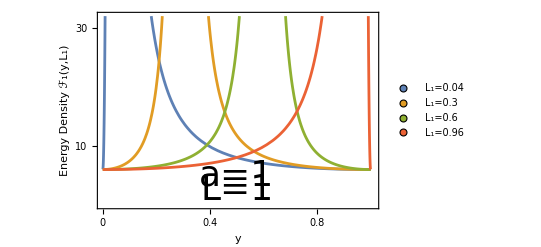

```mathematica
f[a_,L_,L1_,x_]:=(4×a^2)/L^2+a^2/(2×L^2)×((Csc[(π×(x-L1))/(2×L)])^2+(Cos[(π×(x-3×L1))/(2×L)]-Cos[(π×(x+L1))/(2×L)])×Cot[(π×L1)/L]×(Csc[(π×(x-L1))/(2×L)])^2×Csc[(π×(x+L1))/(2×L)]+(Csc[(π×(x+L1))/(2×L)])^2);
Plot[{f[1,1,0.04,x],f[1,1,0.3,x],f[1,1,0.6,x],f[1,1,0.96,x]},{x,0,1},PlotStyle->Thickness[0.005],Frame->{True, True, True, True}, FrameTicks->{{{10,20,30,40,50,60,70},None},{{0,0.2, 0.4, 0.6, 0.8,1.0},None}},PlotRange->{{0,1.01},{0,32}},FrameLabel->{{"Energy Density ℱ_1(y,L_1)", None},{"y", None}},FrameTicksStyle->Directive[Black,36],FrameStyle->Thickness[0.005],LabelStyle->Directive[Black,32],PlotLegends->Placed[PointLegend[{"L_1=0.04","L_1=0.3","L_1=0.6","L_1=0.96","L_1=0.96"},LegendMarkers->{{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12},{Graphics[Disk[]],12}}],{Left, Top}],Epilog->{Text[Style["a=1",Directive[Black,36]],{0.5,5}],Text[Style["L=1",Directive[Black,36]],{0.5,2.5}]}]
```